```mathematica
(* 可视化一维数字列表 *)
{1，4，9，16，25};
```

```mathematica
data = {1,4,9,16,25};
```

```mathematica
data
```

{1,4,9,16,25}

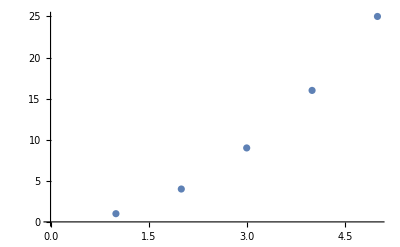

-Graphics-

```mathematica
ListPlot[data]
```

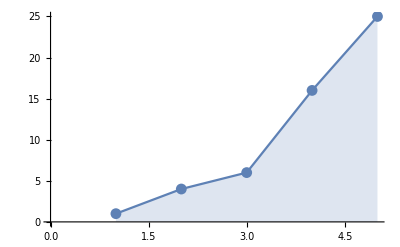

```mathematica
ListLinePlot[{1,4,6,16,25},Mesh->All,Filling->Bottom] (* ListLinePlot指令将散点图中的点顺次链接 *)
```

```mathematica
Manipulate[
	Iplot[data],
	{Iplot,{ListPlot,ListLinePlot,ListLogPlot,ListLogLogPlot}},
	Initialization:>{data= {1,2,3}}(* 初始化Iplot的参数data，其中Iplot是备选函数的别名 *)
]
```

ListPlot::lpn: data 不是由数字或者数对组成的列表.

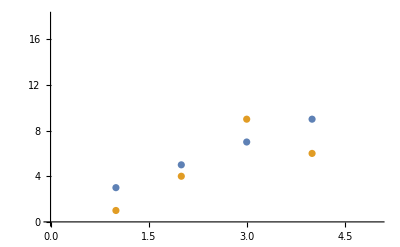

```mathematica
(* 绘制多个数据集 *)
ListPlot[{
	{3,5,7,9},
	{1,4,9,6,25}
}]
```

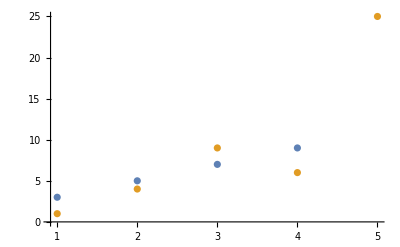

```mathematica
(* 显示点集的整个范围 *)
ListPlot[{{3,5,7,9},{1,4,9,6,25}},PlotRange->All]
```

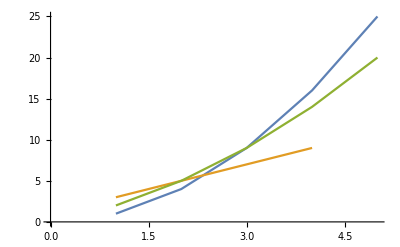

```mathematica
dataset1 = {1,4,9,16,25};
dataset2 = {3,5,7,9};
dataset3 = {2,5,9,14,20};
ListLinePlot[{dataset1,dataset2,dataset3}]
```

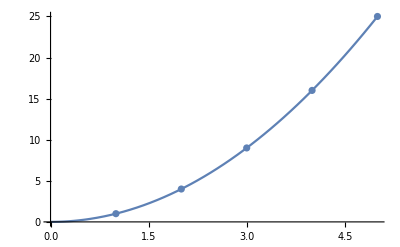

```mathematica
(* 基于Show函数将不同的函数图形组合起来 *)
Show[Plot[x^2,{x,0,5}],ListPlot[{1,4,9,16,25}]]
```

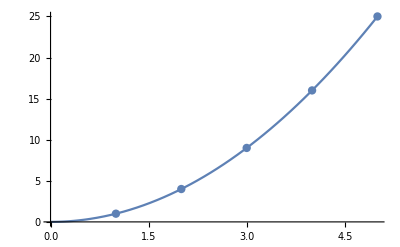

```mathematica
Show[Plot[x^2,{x,0,5}],ListPlot[{1,4,9,16,25},PlotStyle->{"Red",PointSize[0.015]}]]
```

```mathematica
(* 可视化二维数字列表 *)
ListPlot[{1,4,9,16,25}]
```

-Graphics-

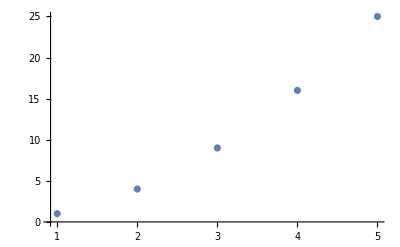

```mathematica
ListPlot[{{1,1},{2,4},{3,9},{4,16},{5,25}}]
```

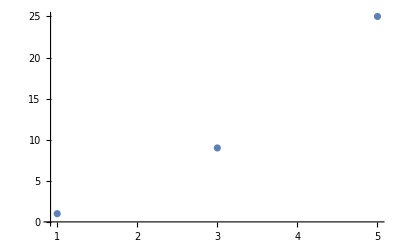

```mathematica
ListPlot[{{1,1},{3,9},{5,25}}]
```

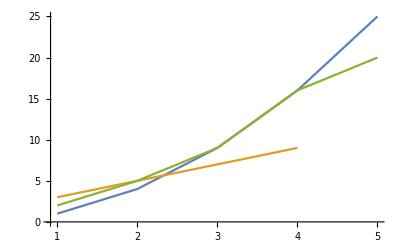

```mathematica
dataset1= {{1,1},{2,4},{3,9},{4,16},{5,25}};
dataset2 = {{1,3},{2,5},{3,7},{4,9}};
dataset3 = {{1,2},{2,5},{3,9},{4,16},{5,20}};
ListLinePlot[{dataset1,dataset2,dataset3}]
```

```mathematica
Manipulate[
ListPlot[Table[{n,Prime[n]},{n,1,max,1}]],
{max,1,50,1}
]
```

```mathematica
(*  可视化三维数字列表 *)
data3 = Table[
	N[Sin[x]Cos[y]],{x,-3,3,0.01},{y,-3,3,0.01}
];
```

```mathematica
ListPlot3D[data3]
```

-Graphics3D-

```mathematica
data3 = Table[
	N[Sin[x]Cos[y]],{x,-3,3,0.1},{y,-3,3,0.1}
];
ListPointPlot3D[data3]
```

-Graphics3D-

```mathematica
Manipulate[
func[Table[N[Sin[x]Cos[y],10],{x,-3,3,incr},{y,-3,3}]],
{{incr,1,"step size"},1,0.05},
{{func,ListPointPlot3D,"function"},{ListPlot3D,ListLinePlot3D}}
]
```

```mathematica
(* 与上一个输出等价的操作 *)
Manipulate[
func[data],
{{incr,1,"step size"},1,0.05},
{{func,ListPointPlot3D,"function"},{ListPlot3D,ListLinePlot3D}},
Initialization:>{data=Table[N[Sin[x]Cos[y],10],{x,-3,3,incr},{y,-3,3}]} (* 这里初始化的时候要加上括号 *)
]
```

ListPointPlot3D::ldata: data 不是一个有效的数据集或者数据集列表.

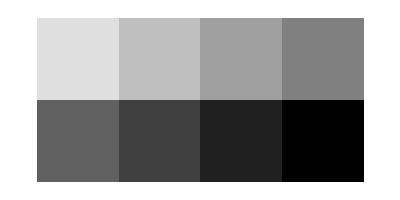

```mathematica
(* 可视化矩阵 *)
ArrayPlot[{
	{1,2,3,4},
	{5,6,7,8}
}]
```

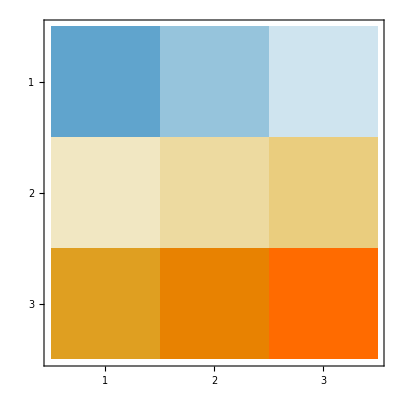

```mathematica
MatrixPlot[
	{
	{-10,-5,-1},
	{2,4,6},
	{20,30,40}
}
]
```

```mathematica
d = RandomInteger[{-100,100},{25,25}];
```

```mathematica
Show[MatrixPlot[d],ArrayPlot[d,Frame->False]] (* 这将导致两张图中后者覆盖前者 *)
```

-Graphics-

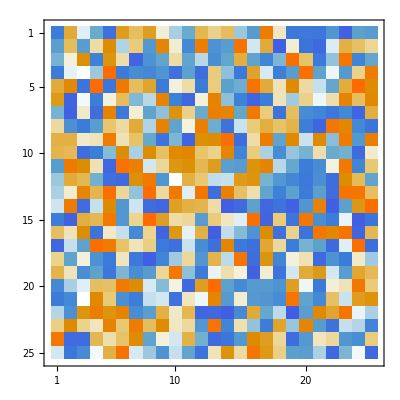
{-Graphics-,-Graphics-}

```mathematica
{MatrixPlot[d],ArrayPlot[d,Frame->False]}
```

```mathematica
(* 与地理有关的图形 *)
GeoGraphics[Point[GeoPosition[{37.2969,-121.819}]]]
```

-Graphics-

```mathematica
GeoGraphics[{Purple,PointSize[Large],Point[GeoPosition[{37.2969,-121.819}]]}]
```

-Graphics-

```mathematica
GeoGraphics[{
Red,
PointSize[Large],
Point[GeoPosition[{37.7699,-122.226}]],
Point[GeoPosition[{37.2969,-121.819}]],
Point[GeoPosition[{37.7599,-122.437}]]
}]
```

-Graphics-

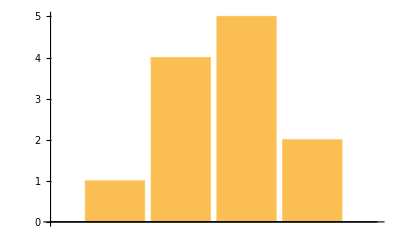

```mathematica
(* 用图表来可视化数据 *)
BarChart[{1,4,5,2}]
```

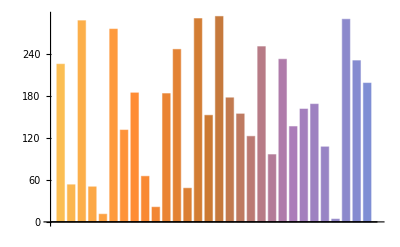

```mathematica
BarChart[{RandomInteger[{1,300},30]}]
```

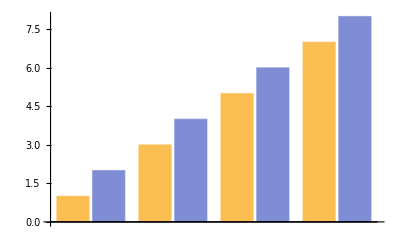

```mathematica
BarChart[{
{1,2},{3,4},{5,6},{7,8}
}]
```

```mathematica
Manipulate[
function[{{1,2},{3,4},{5,6},{7,8}}],
{function,{PieChart,PieChart3D,SectorChart,BarChart,BarChart3D}}
]
```

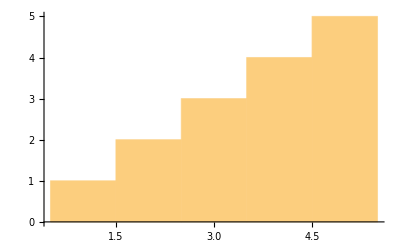

```mathematica
Histogram[{1,2,2,3,3,3,4,4,4,4,5,5,5,5,5}]
```

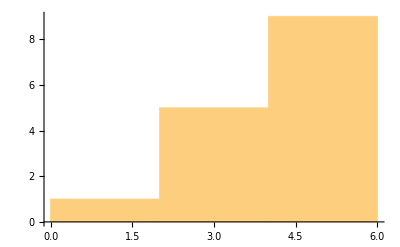

```mathematica
(* 对直方图手动选择组距 *)
Histogram[{1,2,2,3,3,3,4,4,4,4,5,5,5,5,5},3]
```

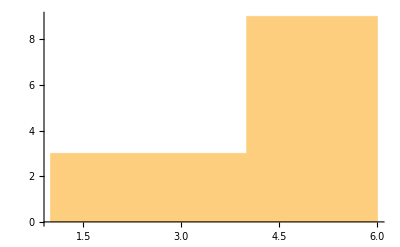

```mathematica
Histogram[{1,2,2,3,3,3,4,4,4,4,5,5,5,5,5},{{1,3,4,6}}]
```

```mathematica
cloudNum = RandomInteger[{1,10},10];
WordCloud[cloudNum]
```

-Graphics-

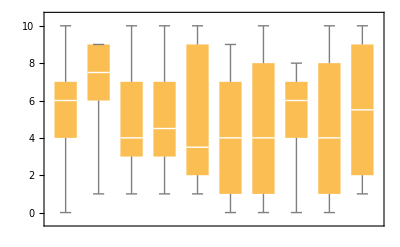

```mathematica
BoxWhiskerChart[RandomInteger[{0,10},{10,10}]]
```

```mathematica
Clear[data,dataset1,dataset2,dataset3,data3,d,cloudNum]
```